```mathematica
v=246;
mhpole=125.13;
ΓSM=4.07*10^-3;(*GeV*)
A[mS_,sinθ_]:=((mhpole^2-mS^2)sinθ √(1-sinθ^2))/v;
λhL[mS_,sinθ_]:=((1-sinθ^2)mhpole^2+sinθ^2 mS^2)/(2 v^2);
ghSS[mS_,sinθ_]:=A[mS,sinθ]sinθ+6λhL[mS,sinθ]v sinθ^2;
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mhpole)√(1-4 mS^2/mhpole^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
```

```mathematica
BRhSS[5,0.03]
```

0.00101873

```mathematica
prospectdata=Import[NotebookDirectory[]<>"Exoticdecay.csv"];
prospectfunc[mS_]:=Interpolation[prospectdata][mS];
```

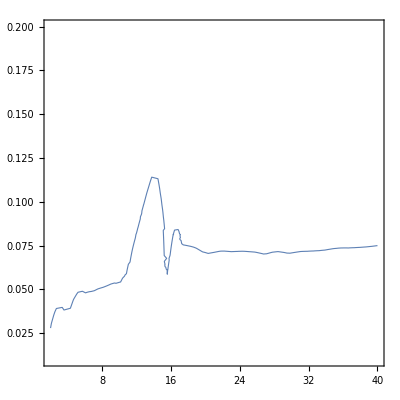

```mathematica
ContourPlot[BRhSS[mS,sinθ]==prospectfunc[mS],{mS,2,40},{sinθ,0.01,0.2}]
```

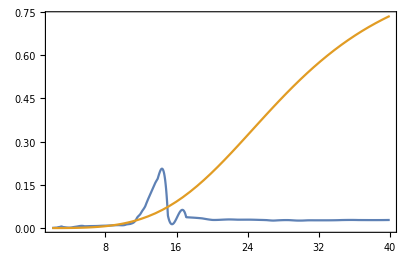

```mathematica
Plot[{prospectfunc[mS],BRhSS[mS,0.006mS]},{mS,2,40}]
```